```mathematica
(* Convolution of the projection of coadjoint orbits of SU(2) 

	Subscript[μ, Subscript[λ, 1]]*...*Subscript[μ, Subscript[λ, n]]= ∫_(t^+) ∑_w sgn(w) Subscript[e, w.Subscript[λ, 1]] * Subscript[μ^p, Subscript[λ, 2]]*...*Subscript[μ^p, Subscript[λ, n]](λ'') Subscript[μ, λ'']  dλ'' 
and
   Subscript[μ^p, Subscript[λ, 1]]*...*Subscript[μ^p, Subscript[λ, n]]= ∫_(t^+) ∑_w sgn(w) Subscript[e, w.Subscript[λ, 1]] * Subscript[μ^p, Subscript[λ, 2]]*...*Subscript[μ^p, Subscript[λ, n]](λ'') Subscript[μ^p, λ'']  dλ''
  *)
ClearAll["Global`*"]
```

```mathematica
(*1. Specify the continuous Kostant function P *)
f[x_]:=Piecewise[{{1, 0<=x<∞}},0];
```

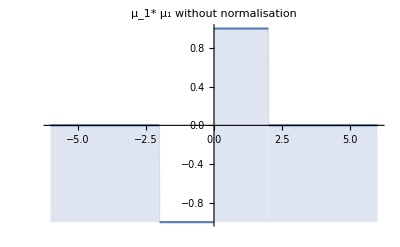

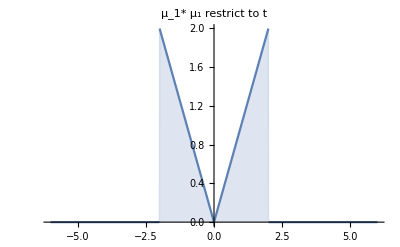

```mathematica
(*2. write down convolution formula *)
λ1=1; λ2=1;
ϕ[x_]:=( ∑_(i=1)^2 ∑_(j=1)^2 (-1)^(i+j) *f[  (-1)^(i+1)  λ1  -(-1)^(j+1)λ2+ x ]);    (* ν(1,1,λ'') *)
ϕ1[x_]:=( ∑_(i=1)^2 ∑_(j=1)^2 (-1)^(i+j+2) *f[ (-1)^(i+1)  λ1 - (-1)^(j+1)  λ2 + x ])*x;
Plot[ϕ[x],{x,-6,6},Filling->Bottom,PlotLabel->"μ_1* μ_1 without normalisation"]
Plot[ϕ1[x],{x,-6,6},Filling->Bottom,PlotLabel->"μ_1* μ_1 restrict to t"]
```

```mathematica
ϕ1[h]//Simplify
```

Piecewise[{{-h, -2≤h<0}, {h, 0≤h<2}, {0, True}}]

```mathematica
D[ϕ1[h],h]//Simplify
```

Piecewise[{{-1, -2<h<0}, {1, 0<h<2}, {0, h>2||h<-2}, {Indeterminate, True}}]

```mathematica
ϕ[h]-3/2 D[h ϕ[h], h]+1/2 D[h D[h ϕ[h], h],h]//Simplify
```

Piecewise[{{0, h≠-2&&h≠0&&h≠2}, {Indeterminate, True}}]

```mathematica
2 (Sin[r]/r)^2+3 r D[(Sin[r]/r)^2,r]+r D[r D[(Sin[r]/r)^2,r],r]//Simplify
```

2 Cos[2 r]

```mathematica
(* Calculate the character formula as a measure*)
```

```mathematica
3 ϕ[h] - 9/2 D[h ϕ[h], h] + 3/2 D[h D[h ϕ[h], h],h] -2   D[D[ ϕ[h],h],h]//Simplify
```

Piecewise[{{0, h≠-2&&h≠0&&h≠2}, {Indeterminate, True}}]

```mathematica
D[ ϕ[h],h]//Simplify
```

Piecewise[{{0, h≠-2&&h≠0&&h≠2}, {Indeterminate, True}}]

```mathematica
D[D[ ϕ[h],h],h]//Simplify
```

Piecewise[{{0, h≠-2&&h≠0&&h≠2}, {Indeterminate, True}}]

```mathematica
9/2 D[h ϕ[h], h]//Simplify
```

Piecewise[{{-9/2, -2<h<0}, {9/2, 0<h<2}, {0, h>2||h<-2}, {Indeterminate, True}}]

```mathematica
3 ϕ[h]//Simplify
```

Piecewise[{{-3, -2≤h<0}, {3, 0≤h<2}, {0, True}}]

```mathematica
3/2 D[h D[h ϕ[h], h],h]//Simplify
```

Piecewise[{{-3/2, -2<h<0}, {3/2, 0<h<2}, {0, h>2||h<-2}, {Indeterminate, True}}]

```mathematica
ϕ[h]//Simplify
```

Piecewise[{{-1, -2≤h<0}, {1, 0≤h<2}, {0, True}}]

```mathematica
3 ϕ1[h] - 9/2 D[h ϕ1[h], h] + 3/2 D[h D[h ϕ1[h], h],h] - 2 D[D[ ϕ1[h],h],h]//Simplify
```

Piecewise[{{0, h≠-2&&h≠0&&h≠2}, {Indeterminate, True}}]

```mathematica
D[ ϕ1[h],h]//Simplify
```

Piecewise[{{-1, -2<h<0}, {1, 0<h<2}, {0, h>2||h<-2}, {Indeterminate, True}}]

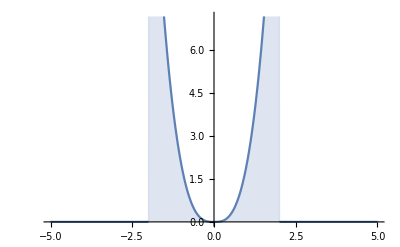

```mathematica
f1[h_]:=Piecewise[{{-2 h^3, -2<h<0}, {2 h^3, 0<h<2}, {0, h>2||h<-2}, {Indeterminate, True}}];
Plot[f1[h],{h,-5,5},Filling->Bottom]
```

```mathematica
f2[h_]:=Piecewise[{{1, h==1}},0];
f2[h]
```

Piecewise[{{1, h==1}, {0, True}}]

```mathematica
f2[1]
```

1

```mathematica
Integrate[f[y]*f2[x-y],{y,0,2}]//Simplify
```

0

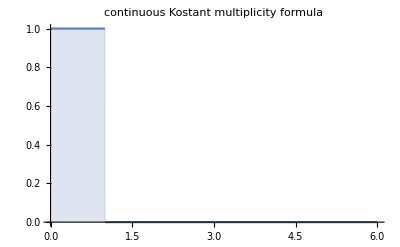

```mathematica
(* Test out Kostant Multiplicity Formula *)
ff[x_,n_]:=-(f[x-n]-f[x+n+1]);
Plot[ff[x,1],{x,0,6},Filling->Bottom,PlotLabel->"continuous Kostant multiplicity formula"]
```

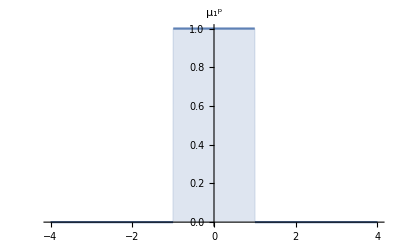

```mathematica
(*Projection of Subscript[μ, 1]:  Subscript[μ, 1]^p   *)
ψ[x_]:= ∑_(i=1)^2 (-1)^(i+1) *f[ (-1)^(i+1)  * 1 - x ];
Plot[ψ[x],{x,-4,4},Filling->Bottom,PlotLabel->"μ_1^p"]
```

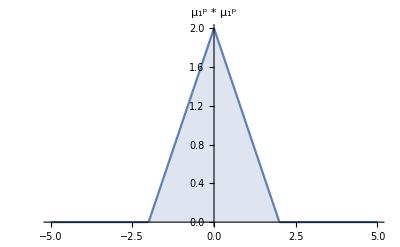

```mathematica
(* Convolution of Projection of Measures Subscript[μ, 1]^p * Subscript[μ, 1]^p  *)
ff[x_]:=Piecewise[{{1,0<x<∞}}];
ϕ2[x_,λ_]:=∑_(i=1)^2 (-1)^(i+1) *ff[ (-1)^(i+1)  λ - x ];
T[x_]=Integrate[ϕ[y]*ϕ2[x,y],{y,0,∞}];
Plot[T[x],{x,-5,5},Filling->Bottom,PlotLabel->"μ_1^p * μ_1^p"]
```

```mathematica
T[x]
```

Piecewise[{{2-x, 0≤x<2}, {2+x, -2<x<0}, {0, True}}]

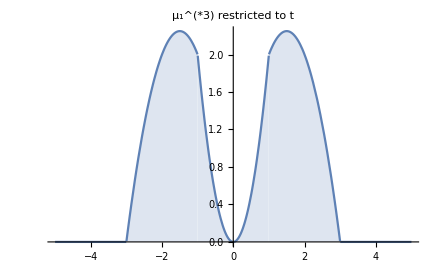

```mathematica
(* Convolution of of Measures Subscript[μ, 1]^(*3) *)
ϕ3[x_]:=∑_(i=1)^2 (-1)^(i+1)*T[(-1)^(i+1)-x]*x;
Plot[ϕ3[x],{x,-5,5},Filling->Bottom,PlotLabel->"μ_1^(*3) restricted to t"]
```

```mathematica
ϕ3[x]//Simplify
```

Piecewise[{{-((-3+x) x), 1≤x<3}, {2 x^2, -1<x<1}, {-x (3+x), -3<x≤-1}, {0, True}}]

```mathematica
(* Calculate character as a measure
	4+(22 dγ)/3+4 dγ^2+(2 dγ^3)/3+10 h^2+(10 dγ h^2)/3+10 x^2+(10 dγ x^2)/3+10 y^2+(10 dγ y^2)/3
*)
```

```mathematica
4*ϕ3[h]- 22/3 D[h * ϕ3[h],h] + 4 * D[h*D[h * ϕ3[h],h],h ] - 2/3 D[h *D[h*D[h * ϕ3[h],h] ,h],h] -10 *D[D[ ϕ3[h],h] ,h]+ 10/3 D[D[D[h * ϕ3[h],h],h],h]//Simplify
```

Piecewise[{{0, -3<h<-1||-1<h<1||1<h<3||h>3||h<-3}, {Indeterminate, True}}]

```mathematica
4*ϕ3[h]//Simplify
```

Piecewise[{{-4 (-3+h) h, 1≤h<3}, {8 h^2, -1<h<1}, {-4 h (3+h), -3<h≤-1}, {0, True}}]

```mathematica
- 22/3 D[h * ϕ3[h],h]//Simplify
```

Piecewise[{{22 (-2+h) h, 1<h<3}, {-44 h^2, -1<h<1}, {22 h (2+h), -3<h<-1}, {0, h>3||h<-3}, {Indeterminate, True}}]

```mathematica
4 * D[h*D[h * ϕ3[h],h],h ] //Simplify
```

Piecewise[{{72 h^2, -1<h<1}, {-12 h (-4+3 h), 1<h<3}, {-12 h (4+3 h), -3<h<-1}, {0, h>3||h<-3}, {Indeterminate, True}}]

```mathematica
- 2/3 D[h *D[h*D[h * ϕ3[h],h] ,h],h]//Simplify
```

Piecewise[{{-36 h^2, -1<h<1}, {2 h (-8+9 h), 1<h<3}, {2 h (8+9 h), -3<h<-1}, {0, h>3||h<-3}, {Indeterminate, True}}]

```mathematica
-10 *D[D[ ϕ3[h],h] ,h]//Simplify
```

Piecewise[{{-40, -1<h<1}, {20, -3<h<-1||1<h<3}, {0, h>3||h<-3}, {Indeterminate, True}}]

```mathematica
10/3 D[D[D[h * ϕ3[h],h],h],h]//Simplify
```

Piecewise[{{-20, -3<h<-1||1<h<3}, {40, -1<h<1}, {0, h>3||h<-3}, {Indeterminate, True}}]

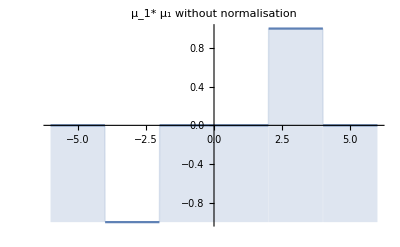

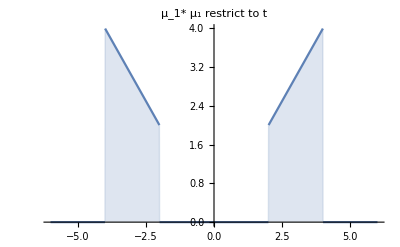

```mathematica
(*2. write down convolution formula *)
λ1=1; λ2=3;
ϕ[x_]:=( ∑_(i=1)^2 ∑_(j=1)^2 (-1)^(i+j) *f[  (-1)^(i+1)  λ1  -(-1)^(j+1)λ2+ x ]);    (* ν(1,1,λ'') *)
ϕ1[x_]:=( ∑_(i=1)^2 ∑_(j=1)^2 (-1)^(i+j+2) *f[ (-1)^(i+1)  λ1 - (-1)^(j+1)  λ2 + x ])*x;
Plot[ϕ[x],{x,-6,6},Filling->Bottom,PlotLabel->"μ_1* μ_1 without normalisation"]
Plot[ϕ1[x],{x,-6,6},Filling->Bottom,PlotLabel->"μ_1* μ_1 restrict to t"]
```

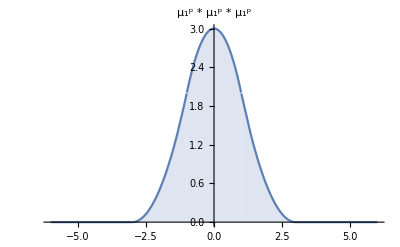

```mathematica
T2[x_]:=∑_(i=1)^2 (-1)^(i+1)*T[(-1)^(i+1)-x];
P[x_]=Integrate[T2[y]*ϕ2[x,y],{y,0,∞}];
Plot[P[x],{x,-6,6},Filling->Bottom,PlotLabel->"μ_1^p * μ_1^p * μ_1^p"]
```

```mathematica
P[x]
```

Piecewise[{{2, x==-1||x==1}, {3-x^2, -1<x<1}, {1/2 (9-6 x+x^2), 1<x<3}, {1/2 (9+6 x+x^2), -3<x<-1}, {0, True}}]

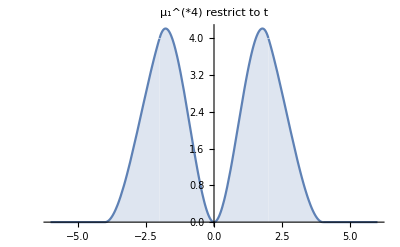

```mathematica
(* Convolution of of Measures Subscript[μ, 1]^(*4) *)
ϕ4[x_]:=∑_(i=1)^2 (-1)^(i+1)*P[(-1)^(i+1)-x]*x;
Plot[ϕ4[x],{x,-6,6},Filling->Bottom,PlotLabel->"μ_1^(*4) restrict to t"]
```

```mathematica
ϕ4[x]//Simplify
```

Piecewise[{{-1/2 x (4+x)^2, -4<x≤-2}, {1/2 (-4+x)^2 x, 2≤x<4}, {1/2 (8-3 x) x^2, 0<x<2}, {1/2 x^2 (8+3 x), -2<x<0}, {0, True}}]

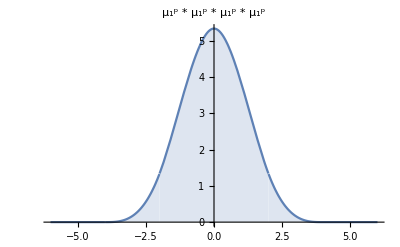

```mathematica
(* Convolution of Projection of Measures Subscript[μ, 1]^p * Subscript[μ, 1]^p * (Subscript[μ, 1]* Subscript[μ, 1])^p *)
T3[x_]:=∑_(i=1)^2 (-1)^(i+1)*P[(-1)^(i+1)-x];
P2[x_]=Integrate[T3[y]*ϕ2[x,y],{y,0,∞}];
Plot[P2[x],{x,-6,6},Filling->Bottom,PlotLabel->"μ_1^p * μ_1^p * μ_1^p * μ_1^p"]
```

```mathematica
P2[x]
```

Piecewise[{{4/3, x==-2||x==2}, {1/6 (32-12 x^2-3 x^3), -2<x<0}, {1/6 (64-48 x+12 x^2-x^3), 2<x<4}, {1/6 (64+48 x+12 x^2+x^3), -4<x<-2}, {1/6 (32-12 x^2+3 x^3), 0≤x<2}, {0, True}}]

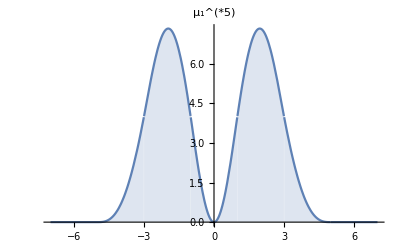

```mathematica
(* Convolution of of Measures Subscript[μ, 1]^(*5) *)
ϕ5[x_]:=∑_(i=1)^2 (-1)^(i+1)*P2[(-1)^(i+1)-x]*x;
Plot[ϕ5[x],{x,-7,7},Filling->Bottom,PlotLabel->"μ_1^(*5)"]
```

```mathematica
ϕ5[x]//Simplify
```

Piecewise[{{-1/6 x (5+x)^3, -5<x≤-3}, {-1/6 (-5+x)^3 x, 3≤x<5}, {-x^2 (-5+x^2), -1≤x≤1}, {1/3 x (-5+30 x-15 x^2+2 x^3), 1<x<3}, {1/3 x (5+30 x+15 x^2+2 x^3), -3<x<-1}, {0, True}}]